```mathematica
f[n_, k_ ] := Sum[ (-1)^(j+1) f[n/j,k-1],{j,2,n}];f[n_,0]:=1
lin[n_]:=Sum[ (-1)^(k+1)/k f[n,k],{k,1,Log[2,n]}]
```

```mathematica
Table[ {n,lin[n]-lin[n-1]},{n,2,100}]//TableForm
```

2 | -1
3 | 1
4 | -3/2
5 | 1
6 | 0
7 | 1
8 | -7/3
9 | 1/2
10 | 0
11 | 1
12 | 0
13 | 1
14 | 0
15 | 0
16 | -15/4
17 | 1
18 | 0
19 | 1
20 | 0
21 | 0
22 | 0
23 | 1
24 | 0
25 | 1/2
26 | 0
27 | 1/3
28 | 0
29 | 1
30 | 0
31 | 1
32 | -31/5
33 | 0
34 | 0
35 | 0
36 | 0
37 | 1
38 | 0
39 | 0
40 | 0
41 | 1
42 | 0
43 | 1
44 | 0
45 | 0
46 | 0
47 | 1
48 | 0
49 | 1/2
50 | 0
51 | 0
52 | 0
53 | 1
54 | 0
55 | 0
56 | 0
57 | 0
58 | 0
59 | 1
60 | 0
61 | 1
62 | 0
63 | 0
64 | -21/2
65 | 0
66 | 0
67 | 1
68 | 0
69 | 0
70 | 0
71 | 1
72 | 0
73 | 1
74 | 0
75 | 0
76 | 0
77 | 0
78 | 0
79 | 1
80 | 0
81 | 1/4
82 | 0
83 | 1
84 | 0
85 | 0
86 | 0
87 | 0
88 | 0
89 | 1
90 | 0
91 | 0
92 | 0
93 | 0
94 | 0
95 | 0
96 | 0
97 | 1
98 | 0
99 | 0
100 | 0

```mathematica
CC[n_, c_] := (1/c^2)Sum[ 1,{j,1,c^2 n},{k,1,Floor[c^2 n/j]}]  - 2 (1/c^2) Sum[ 1,{j,1,c},{k,1,Floor[c^2 n/j]}] + Sum[ 1, {j,1,c},{k,1,c}]
```

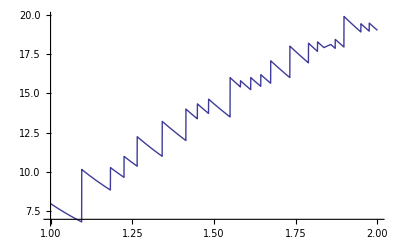

```mathematica
Plot[ CC[ 10,c],{c,1,2}]
```

```mathematica
Sum[ CC[100.,1+cc*.001]-CC[100.,1+(cc-1)*.001],{cc,1,3000}]
```

70.625

```mathematica
CC[100,4.]-CC[100,1]
```

70.625

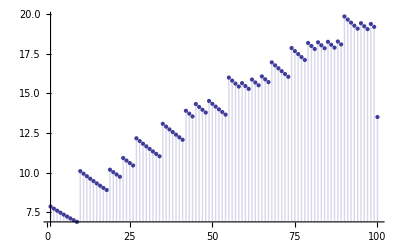

```mathematica
DiscretePlot[ CC[ 10,1+c*.01],{c,1,100}]
```

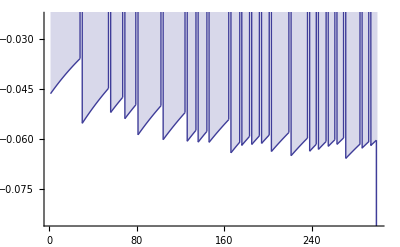

```mathematica
DiscretePlot[ CC[ 10,1+c/300]-CC[ 10,1+(c-1)/300],{c,1,300}]
```

```mathematica
Table[ {10.*(1+c/300.), CC[ 10.,1+c/300.]-CC[ 10,1+(c-1)/300]},{c,1,300}]//TableForm
```

10.0333 | -0.0464344
10.0667 | -0.0459739
10.1 | -0.0455194
10.1333 | -0.045071
10.1667 | -0.0446284
10.2 | -0.0441915
10.2333 | -0.0437604
10.2667 | -0.0433349
10.3 | -0.0429148
10.3333 | -0.0425002
10.3667 | -0.0420909
10.4 | -0.0416868
10.4333 | -0.0412879
10.4667 | -0.040894
10.5 | -0.0405052
10.5333 | -0.0401213
10.5667 | -0.0397422
10.6 | -0.0393678
10.6333 | -0.0389982
10.6667 | -0.0386331
10.7 | -0.0382727
10.7333 | -0.0379166
10.7667 | -0.037565
10.8 | -0.0372177
10.8333 | -0.0368747
10.8667 | -0.0365359
10.9 | -0.0362012
10.9333 | -0.0358706
10.9667 | 3.29037
11. | -0.0553479
11.0333 | -0.054847
11.0667 | -0.0543521
11.1 | -0.0538632
11.1333 | -0.0533801
11.1667 | -0.0529028
11.2 | -0.0524312
11.2333 | -0.0519651
11.2667 | -0.0515046
11.3 | -0.0510494
11.3333 | -0.0505997
11.3667 | -0.0501552
11.4 | -0.0497159
11.4333 | -0.0492817
11.4667 | -0.0488525
11.5 | -0.0484283
11.5333 | -0.048009
11.5667 | -0.0475946
11.6 | -0.0471848
11.6333 | -0.0467798
11.6667 | -0.0463794
11.7 | -0.0459836
11.7333 | -0.0455922
11.7667 | -0.0452053
11.8 | -0.0448228
11.8333 | 1.38384
11.8667 | -0.0520833
11.9 | -0.0516463
11.9333 | -0.0512141
11.9667 | -0.0507867
12. | -0.0503641
12.0333 | -0.0499461
12.0667 | -0.0495328
12.1 | -0.049124
12.1333 | -0.0487197
12.1667 | -0.0483198
12.2 | -0.0479243
12.2333 | -0.047533
12.2667 | 1.28201
12.3 | -0.0539576
12.3333 | -0.0535207
12.3667 | -0.0530885
12.4 | -0.052661
12.4333 | -0.052238
12.4667 | -0.0518195
12.5 | -0.0514055
12.5333 | -0.0509959
12.5667 | -0.0505907
12.6 | -0.0501897
12.6333 | -0.0497929
12.6667 | 1.82041
12.7 | -0.0588142
12.7333 | -0.058353
12.7667 | -0.0578965
12.8 | -0.0574448
12.8333 | -0.0569977
12.8667 | -0.0565553
12.9 | -0.0561175
12.9333 | -0.0556841
12.9667 | -0.0552552
13. | -0.0548307
13.0333 | -0.0544106
13.0667 | -0.0539947
13.1 | -0.0535831
13.1333 | -0.0531756
13.1667 | -0.0527722
13.2 | -0.0523729
13.2333 | -0.0519777
13.2667 | -0.0515864
13.3 | -0.051199
13.3333 | -0.0508155
13.3667 | -0.0504358
13.4 | -0.0500599
13.4333 | 2.16694
13.4667 | -0.060279
13.5 | -0.059833
13.5333 | -0.0593915
13.5667 | -0.0589542
13.6 | -0.0585213
13.6333 | -0.0580925
13.6667 | -0.057668
13.7 | -0.0572476
13.7333 | -0.0568312
13.7667 | -0.0564189
13.8 | -0.0560106
13.8333 | -0.0556062
13.8667 | -0.0552056
13.9 | -0.0548089
13.9333 | -0.054416
13.9667 | -0.0540269
14. | -0.0536415
14.0333 | -0.0532597
14.0667 | -0.0528815
14.1 | -0.0525069
14.1333 | -0.0521358
14.1667 | 1.94131
14.2 | -0.0607503
14.2333 | -0.060324
14.2667 | -0.0599016
14.3 | -0.0594832
14.3333 | -0.0590687
14.3667 | -0.058658
14.4 | -0.0582512
14.4333 | -0.057848
14.4667 | -0.0574486
14.5 | 0.894196
14.5333 | -0.0610193
14.5667 | -0.0606009
14.6 | -0.0601863
14.6333 | -0.0597755
14.6667 | -0.0593684
14.7 | -0.0589649
14.7333 | -0.0585652
14.7667 | -0.058169
14.8 | -0.0577764
14.8333 | 0.851589
14.8667 | -0.0610733
14.9 | -0.0606639
14.9333 | -0.0602581
14.9667 | -0.059856
15. | -0.0594574
15.0333 | -0.0590623
15.0667 | -0.0586707
15.1 | -0.0582826
15.1333 | -0.0578979
15.1667 | -0.0575166
15.2 | -0.0571386
15.2333 | -0.0567639
15.2667 | -0.0563925
15.3 | -0.0560243
15.3333 | -0.0556594
15.3667 | -0.0552975
15.4 | -0.0549389
15.4333 | -0.0545833
15.4667 | -0.0542307
15.5 | 2.44352
15.5333 | -0.0642417
15.5667 | -0.0638294
15.6 | -0.0634207
15.6333 | -0.0630155
15.6667 | -0.0626137
15.7 | -0.0622153
15.7333 | -0.0618203
15.7667 | -0.0614286
15.8 | -0.0610402
15.8333 | 0.338237
15.8667 | -0.0619475
15.9 | -0.0615583
15.9333 | -0.0611723
15.9667 | -0.0607896
16. | -0.0604101
16.0333 | -0.0600337
16.0667 | -0.0596604
16.1 | -0.0592902
16.1333 | 0.709467
16.1667 | -0.0617244
16.2 | -0.0613438
16.2333 | -0.0609663
16.2667 | -0.0605918
16.3 | -0.0602205
16.3333 | -0.0598522
16.3667 | -0.0594869
16.4 | -0.0591245
16.4333 | 0.681826
16.4667 | -0.0614039
16.5 | -0.0610321
16.5333 | -0.0606633
16.5667 | -0.0602975
16.6 | -0.0599347
16.6333 | -0.0595747
16.6667 | -0.0592176
16.7 | -0.0588634
16.7333 | 1.37004
16.7667 | -0.0638378
16.8 | -0.0634582
16.8333 | -0.0630816
16.8667 | -0.0627079
16.9 | -0.0623372
16.9333 | -0.0619695
16.9667 | -0.0616046
17. | -0.0612426
17.0333 | -0.0608834
17.0667 | -0.060527
17.1 | -0.0601734
17.1333 | -0.0598225
17.1667 | -0.0594743
17.2 | -0.0591289
17.2333 | -0.0587861
17.2667 | -0.058446
17.3 | -0.0581085
17.3333 | 1.93927
17.3667 | -0.0651
17.4 | -0.0647263
17.4333 | -0.0643553
17.4667 | -0.0639872
17.5 | -0.063622
17.5333 | -0.0632594
17.5667 | -0.0628997
17.6 | -0.0625426
17.6333 | -0.0621883
17.6667 | -0.0618366
17.7 | -0.0614876
17.7333 | -0.0611412
17.7667 | -0.0607973
17.8 | -0.0604561
17.8333 | -0.0601174
17.8667 | -0.0597813
17.9 | 1.18895
17.9333 | -0.063753
17.9667 | -0.0633985
18. | -0.0630466
18.0333 | -0.0626973
18.0667 | -0.0623506
18.1 | -0.0620064
18.1333 | -0.0616648
18.1667 | 0.544684
18.2 | -0.0632068
18.2333 | -0.0628605
18.2667 | -0.0625167
18.3 | -0.0621753
18.3333 | -0.0618365
18.3667 | -0.0615001
18.4 | -0.0611662
18.4333 | -0.0608347
18.4667 | 0.525974
18.5 | -0.0622903
18.5333 | -0.0619545
18.5667 | -0.0616211
18.6 | -0.0612901
18.6333 | -0.0609615
18.6667 | -0.0606352
18.7 | -0.0603113
18.7333 | 0.509912
18.7667 | -0.0616929
18.8 | -0.0613651
18.8333 | -0.0610395
18.8667 | -0.0607163
18.9 | -0.0603953
18.9333 | -0.0600766
18.9667 | -0.0597601
19. | 1.87961
19.0333 | -0.0659197
19.0667 | -0.0655743
19.1 | -0.0652312
19.1333 | -0.0648906
19.1667 | -0.0645523
19.2 | -0.0642164
19.2333 | -0.0638828
19.2667 | -0.0635515
19.3 | -0.0632225
19.3333 | -0.0628958
19.3667 | -0.0625713
19.4 | -0.0622491
19.4333 | -0.061929
19.4667 | -0.0616112
19.5 | 0.464674
19.5333 | -0.0627755
19.5667 | -0.062455
19.6 | -0.0621366
19.6333 | -0.0618204
19.6667 | -0.0615063
19.7 | -0.0611944
19.7333 | -0.0608845
19.7667 | 0.451297
19.8 | -0.0619931
19.8333 | -0.0616808
19.8667 | -0.0613706
19.9 | -0.0610625
19.9333 | -0.0607564
19.9667 | -0.0604523
20. | -5.56015